Beginning fit process

Processing frequency 140.174

Done in 2.24612 seconds

All fit parameters: {{140.174,{ω1→33.3333,c→0.0001,a→7.,b→0.,w→0.,rSquared→0.961999}}}

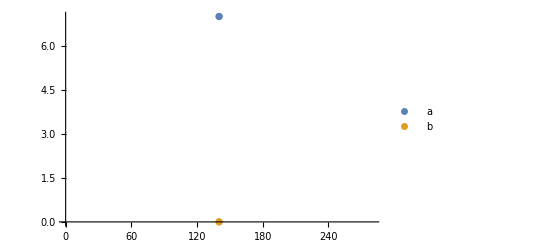

```mathematica
(***** This notebook is for fitting the new thermal mixing model to real data and seeing what happens. *****)
ClearAll["Global`*"];
(* Import the ErrorBarPlots module *)
<< ErrorBarPlots`;

(***** Setup parameters *****)
(* The frequencies to process. Leave this list empty to use all available frequencies. *)
frequenciesToProcess={140.174};
(* The maximum possible steady state. This value will be used to normalize the polarization data. *)
maxSteadyState=0.95;
(* The max time (in seconds) to show on the generated graphs. *)
maxTime=5000;
(* The percent error for each polarization measurement. *)
percentError=0.04;

(***** Thermal mixing model *****)
(* See model.nb for an explanation of this model. *)
subs={nt->np[t]+nm[t],et->ep[t]+em[t],ft->fp[t]+fm[t]};
assumptions={v->1,q->0,r->0,u->0,ce->c/2,cf->c/2};
rates={ω1->0.005,a->5,b->1,w->1};
allRates=assumptions∪rates;
initial={peInit->-1,pfInit->1,pnInit->0};
constants={pe0->-1,pf0->0,pn0->0};
totalTime=5000;
epDot=cf/(ft nt)(-ep[t]fp[t]np[t](r(1-pe0-pf0))
-ep[t]fp[t]nm[t](r(1-pe0-pf0))
-ep[t] fm[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
-ep[t]fm[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+em[t] fp[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
+em[t] fp[t]nm[t](a+u(1+pe0-pf0)+v(1+pe0-pf0))
+em[t]fm[t]np[t](r(1+pe0+pf0))
+em[t]fm[t]nm[t](r(1+pe0+pf0)))ω1;
emDot=-epDot;
fpDot=ce/(et nt)(-fp[t]ep[t]np[t](r(1-pe0-pf0))
-fp[t]ep[t]nm[t](r(1-pe0-pf0))
-fp[t] em[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
-fp[t] em[t]nm[t](a+u(1+pe0-pf0+pn0)+v(1+pe0-pf0))
+fm[t] ep[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
+fm[t]ep[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+fm[t]em[t]np[t](r(1+pe0+pf0))
+fm[t]em[t]nm[t](r(1+pe0+pf0)))ω1;
fmDot=-fpDot;
npDot=ce/(et ft)(-np[t]ep[t]fp[t](q(1-pn0))
-np[t]ep[t]fm[t](a+u(1-pe0+pf0-pn0)+w(1-pn0))
-np[t]em[t]fp[t](b+u(1+pe0-pf0-pn0)+w(1-pn0))
-np[t]em[t]fm[t](q(1-pn0))
+nm[t]ep[t]fp[t](q(1+pn0))
+nm[t]ep[t]fm[t](b+u(1-pe0+pf0+pn0)+w(1+pn0))
+nm[t]em[t]fp[t](a+u(1+pe0-pf0+pn0)+w(1+pn0))
+nm[t]em[t]fm[t](q(1+pn0)))ω1;
nmDot=-npDot;
(* Get expressions for Subscript[P, n], etc. by defining them and eliminating np, nm, etc. *)
peExpr=(ep[t]-em[t])/et/.subs;
pfExpr=(fp[t]-fm[t])/ft/.subs;
pnExpr=(np[t]-nm[t])/nt/.subs;
fnSubs={pn->pn[t],pe->pe[t],pf->pf[t]};
pnDotEqn=pnDot/.Solve[Eliminate[{pnDot==(npDot-nmDot)/nt/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pnDot][[1]]/.fnSubs;
peDotEqn=peDot/.Solve[Eliminate[{peDot==(epDot-emDot)/et/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],peDot][[1]]/.fnSubs;
pfDotEqn=pfDot/.Solve[Eliminate[{pfDot==(fpDot-fmDot)/ft/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pfDot][[1]]/.fnSubs;
eqns={pe'[t]==peDotEqn,pf'[t]==pfDotEqn,pn'[t]==pnDotEqn,pe[0]==peInit,pf[0]==pfInit,pn[0]==pnInit}/.initial;
sol=ParametricNDSolve[eqns/.assumptions/.constants,{pn,pe,pf},{t,0,5000},{ω1,c,a,b,w}];

(***** Fit model to data *****)
timing=AbsoluteTiming[
Print["Beginning fit process"];
(* Calculate the maximum polarization achieved by any of the rampups, and use it to calculate the normalization factor mentioned above *)
SetDirectory[NotebookDirectory[]<>"rampup-data"];
maxSteadyStateInData=Max[Map[Abs[Max[Map[#[[2]]&,Import[#]]]]&,FileNames["*.csv"]]];
steadyStateAdjustment=maxSteadyState/maxSteadyStateInData;

(* The files to iterate over *)
files=If[Length[frequenciesToProcess]==0,
FileNames["*.csv"],
Block[{filesList={},filename},
Do[
filename=ToString[frequency]<>".csv";
If[FileExistsQ[filename],
filesList=Append[filesList,filename],
Print["WARNING: no data available for frequency ",frequency," GHz. Skipping."]
],
{frequency,frequenciesToProcess}];
filesList
]];
(* Collect the fit parameters in this list *)
allFitParameters={};
Do[
frequency=ToExpression[StringDrop[file,-4]];
Print["Processing frequency ",frequency];

(* Get the data from the file and normalize it *)
data=Map[{#[[1]],#[[2]]*steadyStateAdjustment}&,Import[file]];
(* Calculate the errors for each data point and make a list with error bars to plot *)
errors=Map[#[[2]]*percentError&,data];
dataWithErrorBars=MapThread[{#1,ErrorBarPlots`ErrorBar[#2]}&,{data,errors}];

(* Try to fit the model using the given data and errors (errors are assumed to be normally distributed) *)
model=NonlinearModelFit[data,
{pn[ω1,c,a,b,w][t]/.sol,ω1==1/0.03,c==0.0001,0≤a≤7,0≤b≤7,0≤w≤10},
{{ω1,1/0.03},{c,1*^-4},{a,5},{b,1},{w,1}},
t,
Weights->1/errors^2];
(* Get the fit parameters for this frequency and add them to the complete list *)
fitParameters=Join[model["BestFitParameters"],{rSquared->model["AdjustedRSquared"]}];
allFitParameters=Join[allFitParameters,{{frequency,fitParameters}}];

(* Generate some nice plots of the data *)
plotData=ErrorBarPlots`ErrorListPlot[dataWithErrorBars,PlotStyle->PointSize[0.01],PlotRange->{{0,maxTime},{0,1}}];
plotModel=Plot[model[t],{t,0,maxTime},PlotStyle->{{Orange,Thick}},PlotRange->{{0,maxTime},{0,1}}];
plot=Labeled[Show[plotData,plotModel,ImageSize->Large],{ToString[frequency],"Time (s)","Polarization"},{Top,Left,Bottom},RotateLabel->True,ImageMargins->5];
(* Save the plot to a file *)
Export["fit-plots/"<>ToString[frequency]<>".png",plot];,
{file,files}]];
Print["Done in ",timing[[1]]," seconds"];

(* Done processing all files *)
Print["All fit parameters: ",allFitParameters];

(* Make some useful graphs *)
aList=Map[{#[[1]],a/.#[[2]]}&,allFitParameters];
bList=Map[{#[[1]],b/.#[[2]]}&,allFitParameters];
Print[ListPlot[{aList,bList},PlotLegends->{"a","b"}]];
```